QuasiNormalModes > QuasiNormalModes

# QuasiNormalModes

The QuasiNormalModes package provides functions for computing quasinormal modes of Schwarzschild and Kerr black holes. Before using the functions, first load the package

```mathematica
<<QuasiNormalModes`
```

### Computing a specific quasinormal mode

```mathematica
QuasiNormalMode[0,0,0,0, 0]
```

0.110455-0.104896 ⅈ

```mathematica
QuasiNormalMode[0,1,1,0, 0.1](* Slowly rotating Kerr black hole *)
```

0.28557-0.097626 ⅈ

```mathematica
QuasiNormalMode[2,2,0,0, 0](* Gravitational case *)
```

0.373672-0.0889623 ⅈ

### Plotting

The QuasiNormalMode function is listable, allowing for easy computation of a family of QNMs.

```mathematica
Modes=QuasiNormalMode[1, Table[i, {i, 1, 5}], 0, 0, 0] (* First 20 modes for the 0-th overtone *)
```

{0.248263-0.0924877 ⅈ,0.457596-0.0950044 ⅈ,0.656899-0.0956162 ⅈ,0.853095-0.0958599 ⅈ,1.04791-0.0959817 ⅈ}

If you wish to generate a list of lists of QNMs however:

```mathematica
QNMsTable = Table[QuasiNormalMode[1, Table[i, {i, 1, 5}], 0, j, 0], {j, 0, 5}];
```

This can be easily plotted, to allow for checks on the validity of the computed modes, analysing their behaviour, etc.

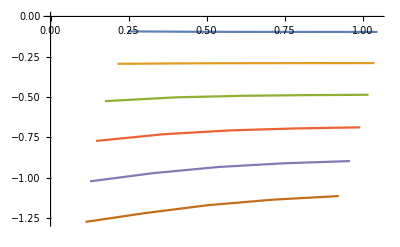

```mathematica
ListPlot[ReIm[QNMsTable], Joined->True]
```

### Conventions

Note that the convention used in this package is M=1. 
In addition, we use a convention where all QNMs are returned in the fourth-quadrant of the complex plane (Re[ω] > 0, Im[ω] < 0).

If necessary, obtaining the QNMs in another quadrant is a simple transformation.

```mathematica
-Conjugate[QNMsTable] (* Third quadrant *)
```

{{-0.248263-0.0924877 ⅈ,-0.457596-0.0950044 ⅈ,-0.656899-0.0956162 ⅈ,-0.853095-0.0958599 ⅈ,-1.04791-0.0959817 ⅈ},{-0.214515-0.293668 ⅈ,-0.436542-0.29071 ⅈ,-0.641737-0.289728 ⅈ,-0.841267-0.289315 ⅈ,-1.03822-0.289104 ⅈ},{-0.174774-0.525188 ⅈ,-0.401187-0.501587 ⅈ,-0.613832-0.492066 ⅈ,-0.818728-0.487838 ⅈ,-1.01944-0.485646 ⅈ},{-0.146177-0.771909 ⅈ,-0.362595-0.730199 ⅈ,-0.577919-0.706331 ⅈ,-0.787748-0.694242 ⅈ,-0.992813-0.687658 ⅈ},{-0.126554-1.02255 ⅈ,-0.328737-0.971609 ⅈ,-0.539769-0.93318 ⅈ,-0.751549-0.910242 ⅈ,-0.960175-0.896747 ⅈ},{-0.112253-1.27393 ⅈ,-0.301493-1.21972 ⅈ,-0.503902-1.17036 ⅈ,-0.713634-1.136 ⅈ,-0.9238-1.1138 ⅈ}}